```mathematica
Clear["Global`*"]
dir=NotebookDirectory[];
K1=-7;
D1=-1.42;
K2=-1.5;
D2=-0.56;
K3=0.04;
D3=0.002;
m=0.086;
g=9.81;
J=1/12 m(0.02^2+0.035^2);
L=0.035;
(*u1max=1.224;
u2max=0.08925L;*)
Fmax=0.612;
scale=4050;
K1=-7;

(*Change between original and new controller*)
D1=-1.42;
K2=-1.5;(*Original:1.5, New:7*)
D2=-1.95;(*Original:1.95, New:3*)
(*Change between original and new controller*)

K3=.04;
D3=.002;
ωmax=19200/60*2π;
ωmin=10000/60*2π;
u11=m g+K1 (y[t]-yp[t])+D1( y'[t]-D[yp[t],t]);
(*ϕdes=Sign[K2 x[t]+D2 x'[t]]*Min[Abs[K2 x[t]+D2 x'[t]],0.2];*)
ϕdes=0.13Tanh[K2 (x[t]-xp[t])+D2 (x'[t]-D[xp[t],t])];
u21=K3(ϕdes-ϕ[t])+D3 (-ϕ'[t]);
(*Eredeti: u21=K3(ϕdes-ϕ[t])+D3 (D[ϕdes,t]-ϕ'[t]);*)
ω11=(u11+2 u21/L)/2 scale;
ω21=(u11-2 u21/L)/2 scale;
ω1=Max[Min[ω11,ωmax],ωmin];
ω2=Max[Min[ω21,ωmax],ωmin];
F1=lift[ω1,x'[t]Cos[ϕ[t]]+y'[t]Sin[ϕ[t]],-y'[t]Cos[ϕ[t]]-x'[t]Sin[ϕ[t]]-L*ϕ'[t]];
F2=lift[ω2,x'[t]Cos[ϕ[t]]+y'[t]Sin[ϕ[t]],-y'[t]Cos[ϕ[t]]-x'[t]Sin[ϕ[t]]+L*ϕ'[t]];
u1=F1+F2;
u2=L/2(F1-F2);

eqs={x''[t]==(u1 Sin[ϕ[t]])/m,y''[t]==-g+(u1 Cos[ϕ[t]])/m,ϕ''[t]==u2/J};
```

```mathematica
(*Simulate the system with both lift models. The params for the lift model are in order: ω,vx,vy*)
liftnew[ω_,vx_,vy_]:=-2*(0.0005917217101953038 vx^2-0.00002557102446913359 vx^4-0.0009764562665337519 vy-0.00013859859899200091 vx^2 vy+0.00004560884655456854 vy^3-7.893807214858706*^-8 ω^2);
liftorig[ω_,vx_,vy_]:=1.5042947579635582*^-7 ω^2;
Simulate[xpa_,ypa_,T_,IC_:{1,0,0,0,0,0}]:=<|
"orig"->NDSolve[(eqs/.{xp->xpa,yp->ypa,lift->liftorig})&&x[0]==IC[[1]]&&y[0]==IC[[2]]&&ϕ[0]==IC[[3]]&&x'[0]==IC[[4]]&&y'[0]==IC[[5]]&&ϕ'[0]==IC[[6]],{x[t],y[t],ϕ[t]},{t,0,T}][[1]],"new"->NDSolve[(eqs/.{xp->xpa,yp->ypa,lift->liftnew})&&x[0]==IC[[1]]&&y[0]==IC[[2]]&&ϕ[0]==IC[[3]]&&x'[0]==IC[[4]]&&y'[0]==IC[[5]]&&ϕ'[0]==IC[[6]],{x[t],y[t],ϕ[t]},{t,0,T}][[1]]|>
(*Plot omegas*)
PlotOmega[sol_,ranges_,onlyoneplot_:False,plotstyle_:{{Blue,Thickness[.008]},{Green,Thickness[.008]},{Red,Dashed,Thickness[.008]},{Orange,Dashed,Thickness[.008]}}]:=(ω1v=ω1/.Flatten[{sol[["new"]],D[sol[["new"]],t],D[D[sol[["new"]],t],t],xp'[t]->D[xp[t],t],yp'[t]->D[yp[t],t]}];
ω1vorig=ω1/.Flatten[{sol[["orig"]],D[sol[["orig"]],t],D[D[sol[["orig"]],t],t],xp'[t]->D[xp[t],t],yp'[t]->D[yp[t],t]}];
ω2v=ω2/.Flatten[{sol[["new"]],D[sol[["new"]],t],D[D[sol[["new"]],t],t],xp'[t]->D[xp[t],t],yp'[t]->D[yp[t],t]}];
ω2vorig=ω2/.Flatten[{sol[["orig"]],D[sol[["orig"]],t],D[D[sol[["orig"]],t],t],xp'[t]->D[xp[t],t],yp'[t]->D[yp[t],t]}];
ωplot1=Plot[{ω1v,ω1vorig,ω2v,ω2vorig},{t,ranges[[1,1]],ranges[[1,2]]},PlotRange->All,Frame->True,FrameLabel->{"t [s]","ω [rad/s]"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},ImageSize->{Automatic,350},PlotStyle->plotstyle,Exclusions->None];
ωplot2=Plot[{ω1v,ω1vorig,ω2v,ω2vorig},{t,ranges[[2,1]],ranges[[2,2]]},PlotRange->All,Frame->True,FrameLabel->{"t [s]"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},ImageSize->{Automatic,350},PlotStyle->plotstyle,Exclusions->None];
Legended[Grid[If[!onlyoneplot,{{ωplot1,ωplot2}},{{ωplot1}}]],Placed[LineLegend[Directive@@@plotstyle,{"ω_1 Data-driven model","ω_1 Base model","ω_2 Data-driven model","ω_2 Base model"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},LegendLayout->"Row"],Below]])
Plotxy[sol_,range_,plotstyle_:{{Blue,Thickness[.008]},{Green,Thickness[.008],Dashing[Large,Large]},{Red,Dashing[Small,Medium],Thickness[.008]}}]:=(xplot=Plot[{x[t]/.sol[["new"]],x[t]/.sol[["orig"]],xp[t]},{t,range[[1]],range[[2]]},PlotRange->All,Frame->True,FrameLabel->{"t [s]","x [m]"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},ImageSize->{Automatic,350},PlotStyle->plotstyle];
yplot=Plot[{y[t]/.sol[["new"]],y[t]/.sol[["orig"]],yp[t]},{t,range[[1]],range[[2]]},PlotRange->All,Frame->True,FrameLabel->{"t [s]","y [m]"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},ImageSize->{Automatic,350},PlotStyle->plotstyle];
Legended[Grid[{{xplot,yplot}}],Placed[LineLegend[Directive@@@plotstyle,{"Data-driven model","Base model","Prescribed"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},LegendLayout->"Row"],Below]])
Plotxyϕ[sol_,range_,plotstyle_:{{Blue,Thickness[.008]},{Green,Thickness[.008],Dashing[Large,Large]},{Red,Dashing[Small,Medium],Thickness[.008]}}]:=(xplot=Plot[{x[t]/.sol[["new"]],x[t]/.sol[["orig"]],xp[t]},{t,range[[1]],range[[2]]},PlotRange->All,Frame->True,FrameLabel->{"t [s]","x [m]"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},ImageSize->{Automatic,350},PlotStyle->plotstyle];
yplot=Plot[{y[t]/.sol[["new"]],y[t]/.sol[["orig"]],yp[t]},{t,range[[1]],range[[2]]},PlotRange->All,Frame->True,FrameLabel->{"t [s]","y [m]"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},ImageSize->{Automatic,350},PlotStyle->plotstyle];
ϕplot=Plot[{ϕ[t]/.sol[["new"]],ϕ[t]/.sol[["orig"]]},{t,range[[1]],range[[2]]},PlotRange->All,Frame->True,FrameLabel->{"t [s]","ϕ [rad]"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},ImageSize->{Automatic,350},PlotStyle->plotstyle];
Legended[Grid[{{xplot,yplot},{ϕplot}}],Placed[LineLegend[Directive@@@plotstyle,{"Data-driven model","Base model","Prescribed"},LabelStyle-> {Black,FontSize->30,FontFamily->"Times"},LegendLayout->"Row"],Below]])
Plottraj[sol_,range_,maxtimeprescribed_,plotstyle_:{{Blue,Thickness[.008]},{Green,Thickness[.008],Dashing[Large,Large]},{Red,Dashing[Small,Medium],Thickness[.008]}}]:=(ParametricPlot[{{x[t],y[t]}/.sol[["new"]],{x[t],y[t]}/.sol[["orig"]],Piecewise[{{{xp[t],yp[t]},t<maxtimeprescribed}},Indeterminate]},{t,range[[1]],range[[2]]},PlotRange->All,Frame->True,FrameLabel->{HoldForm[x" [m]"],HoldForm[y" [m]"]},LabelStyle-> {Black,FontSize->36,FontFamily->"Times"},ImageSize->Large,AspectRatio->1,PlotLegends->{"Data-driven model","Base model","Prescribed"},PlotStyle->plotstyle])
```

```mathematica
L2Norm[fcn_,tmin_,tmax_]:=NIntegrate[fcn^2,{t,tmin,tmax},MaxRecursion->100]
NormedRMSE[fcn_,fcnp_,tmin_,tmax_]:=L2Norm[fcn-fcnp,tmin,tmax]/L2Norm[fcnp,tmin,tmax]
diff[sol_,xp_,yp_,maxtorig_,maxtnew_,mintorig_:0,mintnew_:0,dt_:10^-3]:=<|"orig,x"->NormedRMSE[x[t]/.sol[["orig"]],xp[t],mintorig,maxtorig],"new,x"->NormedRMSE[x[t]/.sol[["new"]],xp[t],mintnew,maxtnew],
"orig,y"->NormedRMSE[y[t]/.sol[["orig"]],yp[t],mintorig,maxtorig],"new,y"->NormedRMSE[y[t]/.sol[["new"]],yp[t],mintnew,maxtnew],
"orig,disp"->NormedRMSE[√((x[t]/.sol[["orig"]])^2+(y[t]/.sol[["orig"]])^2),√(xp[t]^2+yp[t]^2),mintorig,maxtorig],"new,disp"->NormedRMSE[√((x[t]/.sol[["new"]])^2+(y[t]/.sol[["new"]])^2),√(xp[t]^2+yp[t]^2),mintnew,maxtnew]|>*100
```

## Circle

## vel=0.2

<|orig,x→0.0403371,new,x→0.0403377,orig,y→0.00124388,new,y→0.00573917,orig,disp→0.0162113,new,disp→0.0177806|>

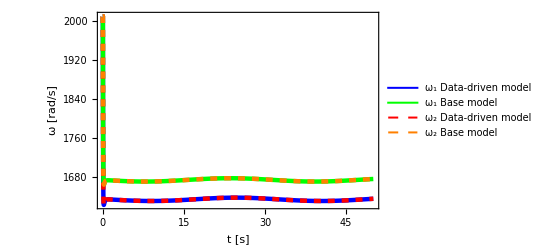

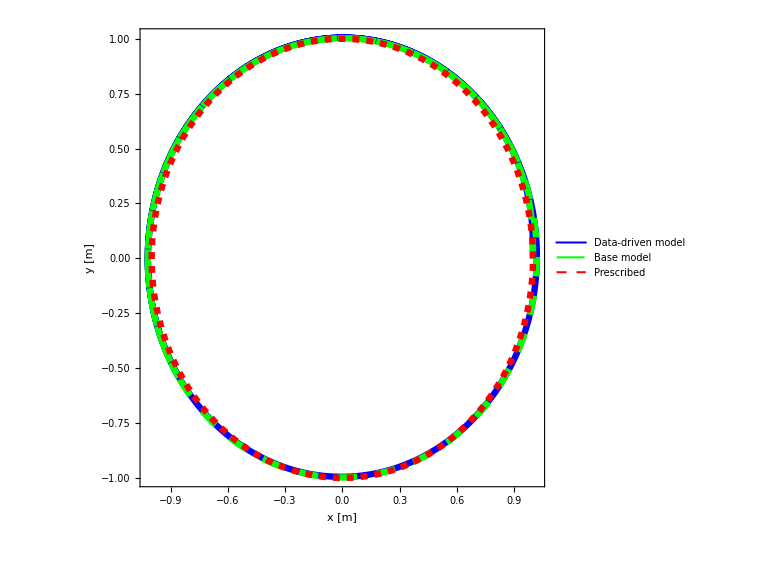

```mathematica
vel=0.2;
T=50;
xp[t_]:=Cos[vel t];
yp[t_]:=Sin[vel t];
sol=Simulate[xp[t],yp[t],T];
diff[sol,xp,yp,T,T]
pocv02=PlotOmega[sol,{{0,T},{2,20}},True,{{Blue,Thickness[.008]},{Green,Thickness[.008]},{Red,Dashed,Thickness[.008]},{Orange,Dashed,Thickness[.008]}}]
ptcv02=Plottraj[sol,{0,T},2 π/vel]
```

```mathematica
Export[FileNameJoin[{dir,"fig/out_circle_orig_omega02.png"}],pocv02,ImageResolution->500];
Export[FileNameJoin[{dir,"fig/out_circle_orig_traj02.png"}],ptcv02,ImageResolution->500];
```

## vel=0.5

<|orig,x→1.29329,new,x→1.29215,orig,y→0.00307753,new,y→0.00718406,orig,disp→0.419908,new,disp→0.422219|>

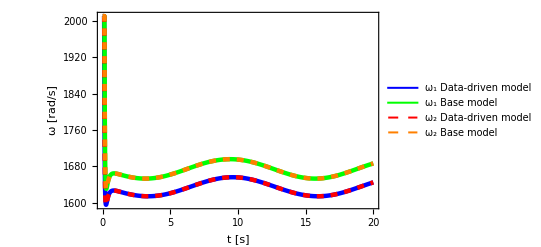

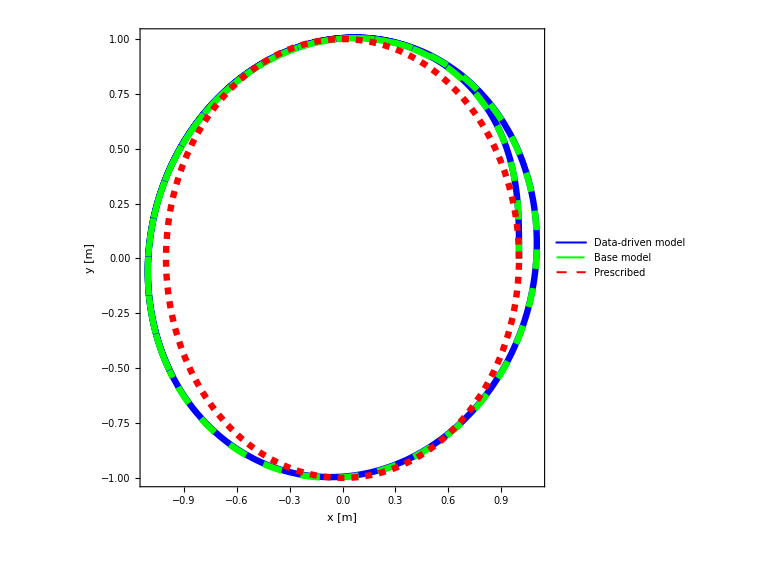

```mathematica
vel=0.5;
T=20;
xp[t_]:=Cos[vel t];
yp[t_]:=Sin[vel t];
sol=Simulate[xp[t],yp[t],T];
diff[sol,xp,yp,T,T]
pocv05=PlotOmega[sol,{{0,T},{2,20}},True,{{Blue,Thickness[.008]},{Green,Thickness[.008]},{Red,Dashed,Thickness[.008]},{Orange,Dashed,Thickness[.008]}}]
ptcv05=Plottraj[sol,{0,T},2 π/vel]
```

```mathematica
Export[FileNameJoin[{dir,"fig/out_circle_orig_omega05.png"}],pocv05,ImageResolution->500];
Export[FileNameJoin[{dir,"fig/out_circle_orig_traj05.png"}],ptcv05,ImageResolution->500];
```

## vel=1

<|orig,x→23.5953,new,x→23.1723,orig,y→0.0755163,new,y→0.0570025,orig,disp→4.07441,new,disp→4.04392|>

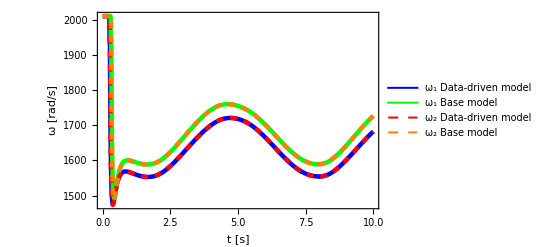

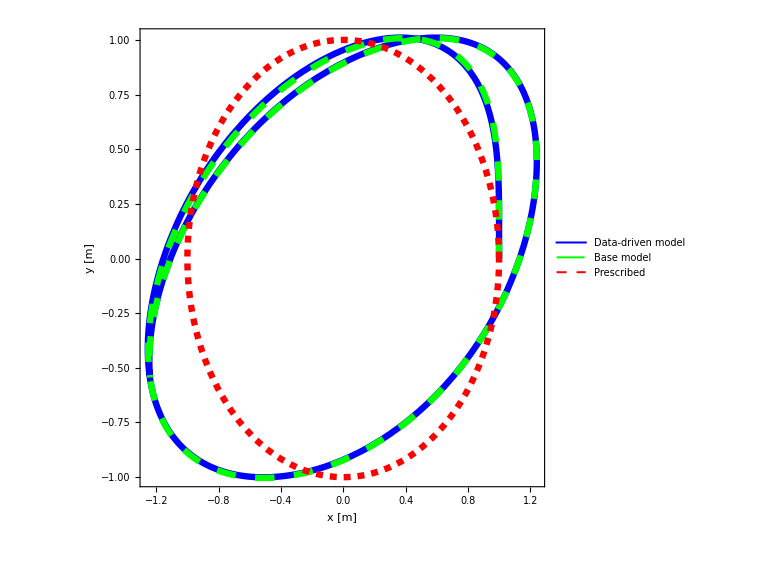

```mathematica
vel=1;
T=10;
xp[t_]:=Cos[vel t];
yp[t_]:=Sin[vel t];
sol=Simulate[xp[t],yp[t],T];
diff[sol,xp,yp,T,T]
pocv1=PlotOmega[sol,{{0,T},{2,20}},True,{{Blue,Thickness[.008]},{Green,Thickness[.008]},{Red,Dashed,Thickness[.008]},{Orange,Dashed,Thickness[.008]}}]
ptcv1=Plottraj[sol,{0,T},2 π/vel]
```

```mathematica
Export[FileNameJoin[{dir,"fig/out_circle_orig_omega1.png"}],pocv1,ImageResolution->500];
Export[FileNameJoin[{dir,"fig/out_circle_orig_traj1.png"}],ptcv1,ImageResolution->500];
```

## Discontinous/sine

## v=1

### SD

<|orig,x→22.6563,new,x→24.8218,orig,y→45.6585,new,y→43.9966,orig,disp→8.15491,new,disp→7.79734|>

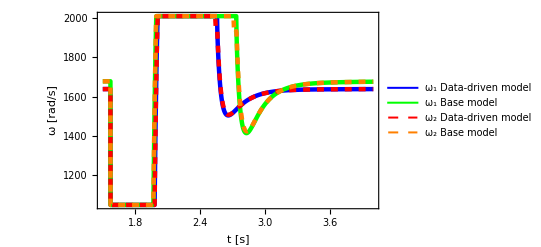

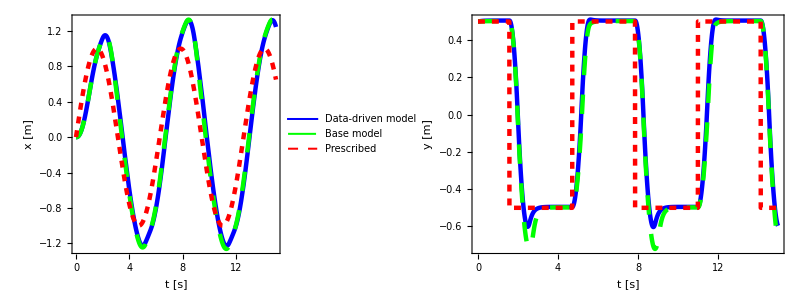

```mathematica
vel=1;
xp[t_]:=Sin[vel t];
yp[t_]:=Piecewise[{{0.5,Cos[vel t]>0},{-0.5,Cos[vel t]<0}}];
T=15;
sol=Simulate[xp[t],yp[t],T,{0,0.5,0,0,0,0}];
diff[sol,xp,yp,T,T]
polv1=PlotOmega[sol,{{1.5,4},{2,T}},True]
pxylv1=Plotxy[sol,{0,T}]
```

```mathematica
Export[FileNameJoin[{dir,"fig/out_Linear_orig_omega1.png"}],polv1,ImageResolution->500];
Export[FileNameJoin[{dir,"fig/out_Linear_orig_disp1.png"}],pxylv1,ImageResolution->500];
```

### DS

<|orig,x→117.712,new,x→117.707,orig,y→0.0481264,new,y→0.0381496,orig,disp→3.05543,new,disp→3.05618|>

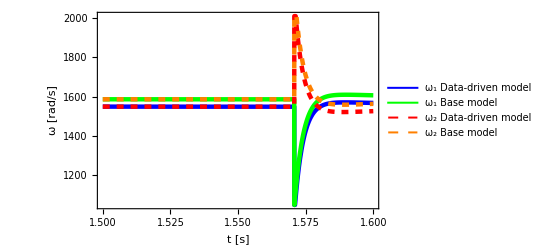

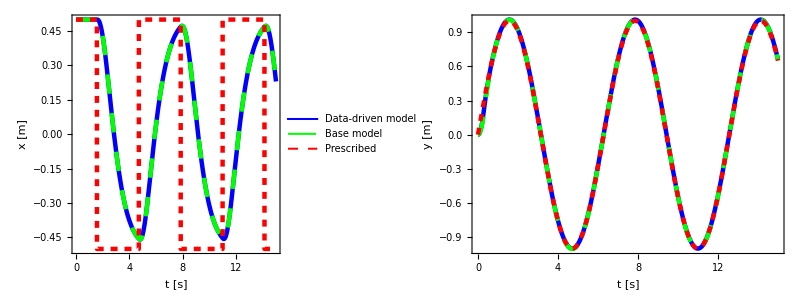

```mathematica
vel=1;
xp[t_]:=Piecewise[{{0.5,Cos[vel t]>0},{-0.5,Cos[vel t]<0}}];
yp[t_]:=Sin[vel t];
T=15;
sol=Simulate[xp[t],yp[t],T,{0.5,0,0,0,0,0}];
diff[sol,xp,yp,T,T]
podsv1=PlotOmega[sol,{{1.5,1.6},{2,T}},True]
pxydsv1=Plotxy[sol,{0,T}]
```

```mathematica
Export[FileNameJoin[{dir,"fig/out_ds_orig_disp1.png"}],pxydsv1,ImageResolution->500];
```

### DD

<|orig,x→256.416,new,x→136.73,orig,y→37.8699,new,y→37.1072,orig,disp→28.9982,new,disp→3.11395|>

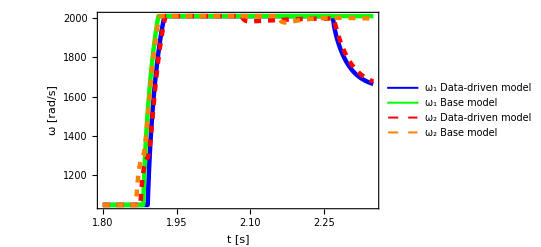

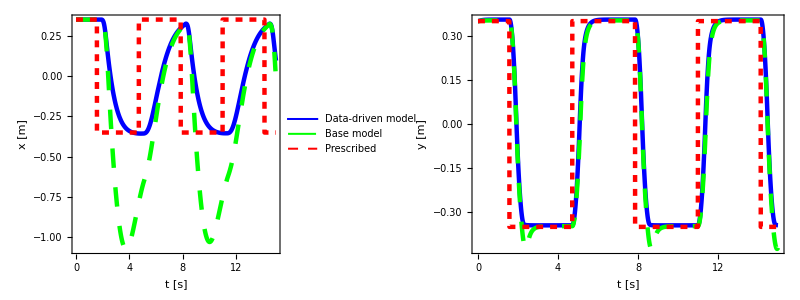

```mathematica
vel=1;
A=0.35;
xp[t_]:=Piecewise[{{A,Cos[vel t]>0},{-A,Cos[vel t]<0}}];
yp[t_]:=Piecewise[{{A,Cos[vel t]>0},{-A,Cos[vel t]<0}}];
T=15;
sol=Simulate[xp[t],yp[t],T,{A,A,0,0,0,0}];
diff[sol,xp,yp,T,T]
poddv1=PlotOmega[sol,{{1.8,2.35},{2,T}},True]
pxyddv1=Plotxy[sol,{0,T}]
```

```mathematica
Export[FileNameJoin[{dir,"fig/out_dd_orig_disp1.png"}],pxyddv1,ImageResolution->500];
```

## v=1.5

### SD

<|orig,x→1224.06,new,x→466.925,orig,y→64.6983,new,y→61.9109,orig,disp→452.573,new,disp→52.1028|>

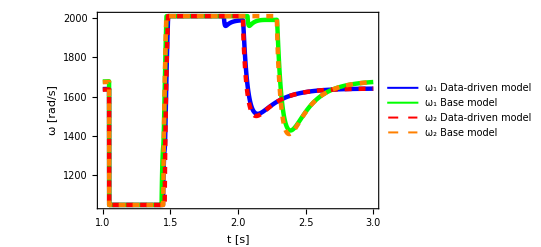

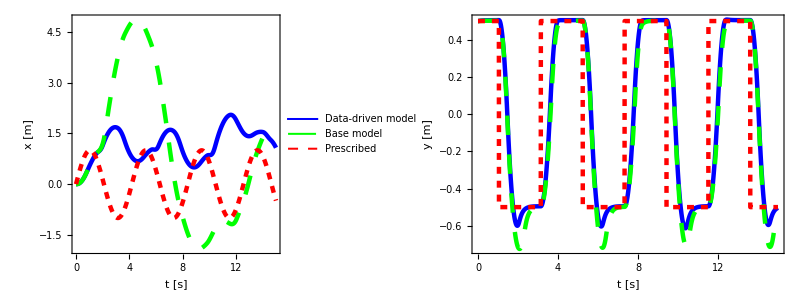

```mathematica
vel=1.5;
xp[t_]:=Sin[vel t];
yp[t_]:=Piecewise[{{0.5,Cos[vel t]>0},{-0.5,Cos[vel t]<0}}];
T=15;
sol=Simulate[xp[t],yp[t],T,{0,0.5,0,0,0,0}];
diff[sol,xp,yp,T,T]
polv15=PlotOmega[sol,{{1,3},{2,T}},True]
pxylv15=Plotxy[sol,{0,T}]
```

```mathematica
Export[FileNameJoin[{dir,"fig/out_Linear_orig_omega15.png"}],polv15,ImageResolution->500];
Export[FileNameJoin[{dir,"fig/out_Linear_orig_disp15.png"}],pxylv15,ImageResolution->500];
```

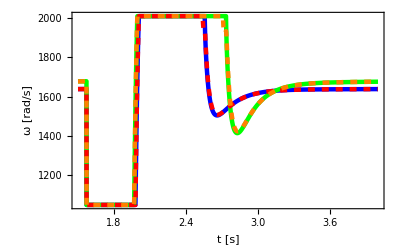

```mathematica
First@polv1
```

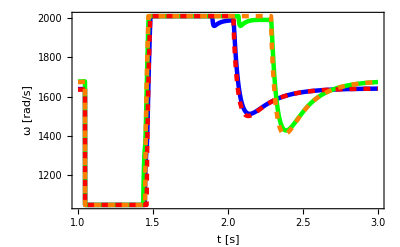
-Graphics- | -Graphics-

```mathematica
polvall=Legended[Grid[{First/@{polv1,polv15}}],Last@polv1]
Export[FileNameJoin[{dir,"fig/out_Linear_orig_omegaall.png"}],polvall,ImageResolution->500];
```

### DS

<|orig,x→151.425,new,x→151.403,orig,y→0.280689,new,y→0.206455,orig,disp→4.38503,new,disp→4.38569|>

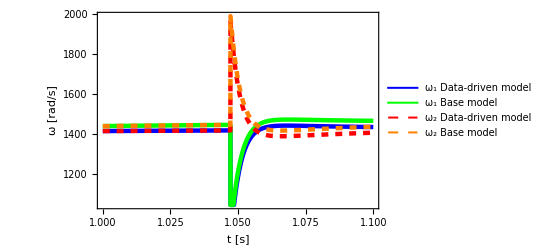

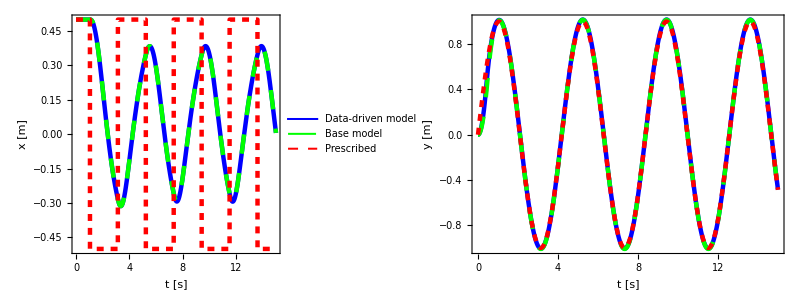

```mathematica
vel=1.5;
xp[t_]:=Piecewise[{{0.5,Cos[vel t]>0},{-0.5,Cos[vel t]<0}}];
yp[t_]:=Sin[vel t];
T=15;
sol=Simulate[xp[t],yp[t],T,{0.5,0,0,0,0,0}];
diff[sol,xp,yp,T,T]
podsv15=PlotOmega[sol,{{1,1.1},{2,T}},True]
pxydsv15=Plotxy[sol,{0,T}]
```

```mathematica
Export[FileNameJoin[{dir,"fig/out_ds_orig_disp15.png"}],pxydsv15,ImageResolution->500];
```

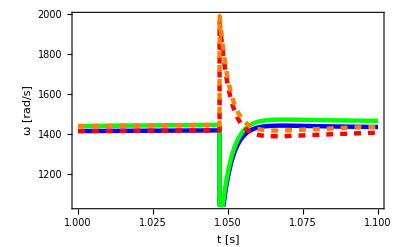
-Graphics- | -Graphics-

```mathematica
podsvall=Legended[Grid[{First/@{podsv1,podsv15}}],Last@podsv1]
Export[FileNameJoin[{dir,"fig/out_ds_orig_omegaall.png"}],podsvall,ImageResolution->500];
```

### DD

<|orig,x→347.888,new,x→171.943,orig,y→53.3955,new,y→51.9841,orig,disp→23.7777,new,disp→6.0036|>

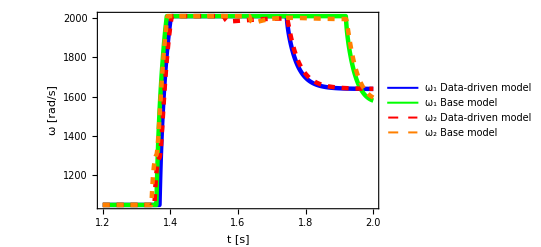

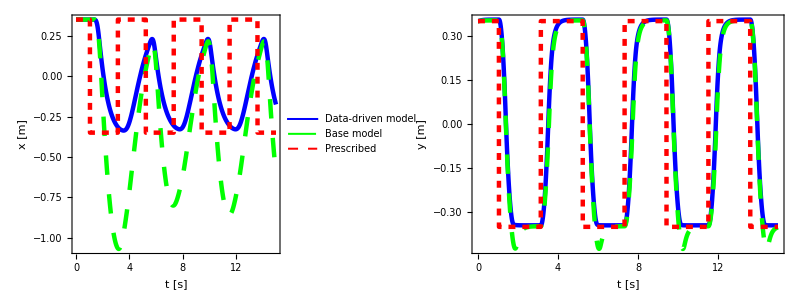

```mathematica
vel=1.5;
A=0.35;
xp[t_]:=Piecewise[{{A,Cos[vel t]>0},{-A,Cos[vel t]<0}}];
yp[t_]:=Piecewise[{{A,Cos[vel t]>0},{-A,Cos[vel t]<0}}];
T=15;
sol=Simulate[xp[t],yp[t],T,{A,A,0,0,0,0}];
diff[sol,xp,yp,T,T]
poddv15=PlotOmega[sol,{{1.2,2},{2,T}},True]
pxyddv15=Plotxy[sol,{0,T}]
```

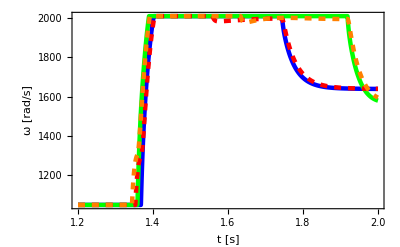
-Graphics- | -Graphics-

```mathematica
Export[FileNameJoin[{dir,"fig/out_dd_orig_disp15.png"}],pxyddv15,ImageResolution->500];
poddvall=Legended[Grid[{First/@{poddv1,poddv15}}],Last@podsv1]
Export[FileNameJoin[{dir,"fig/out_dd_orig_omegaall.png"}],poddvall,ImageResolution->500];
```

## Piecewise linear square

## vel=1

### a=0.4

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

<|orig,x→192.881,new,x→193.712,orig,y→34.2266,new,y→16.9393,orig,disp→15.2056,new,disp→8.61809|>

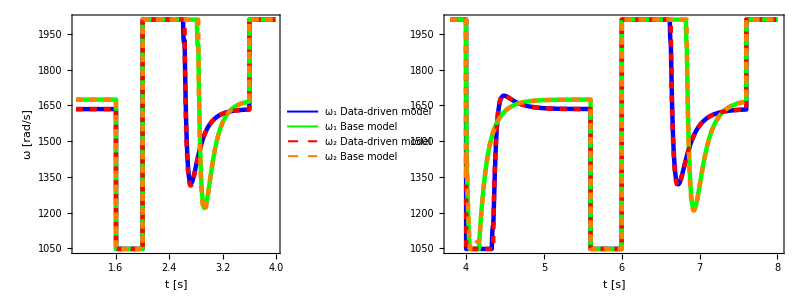

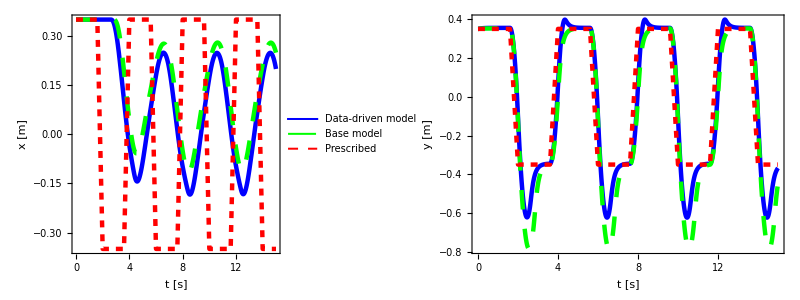

```mathematica
vel=1;
A=0.35;
a=0.4;
xp[t_]:=Interpolation[Flatten[Table[{{2 i/vel,(-1)^i A},{2(i+1)/vel-a,(-1)^i A}},{i,0,IntegerPart[T/2]}],1],t,InterpolationOrder->1]
yp[t_]:=Interpolation[Flatten[Table[{{2 i/vel,(-1)^i A},{2(i+1)/vel-a,(-1)^i A}},{i,0,IntegerPart[T/2]}],1],t,InterpolationOrder->1];
T=15;
sol=Simulate[xp[t],yp[t],T,{A,A,0,0,0,0}];
diff[sol,xp,yp,T,T]
popla04=PlotOmega[sol,{{1,4},{3.8,8}},False]
pxypla04=Plotxy[sol,{0,T}]
```

```mathematica
Export[FileNameJoin[{dir,"fig/out_pl_orig_disp04.png"}],pxypla04,ImageResolution->500];
Export[FileNameJoin[{dir,"fig/out_pl_orig_omega04.png"}],popla04,ImageResolution->500];
```

### a=0.35

<|orig,x→189.628,new,x→184.079,orig,y→17.9209,new,y→14.9296,orig,disp→9.68884,new,disp→8.98427|>

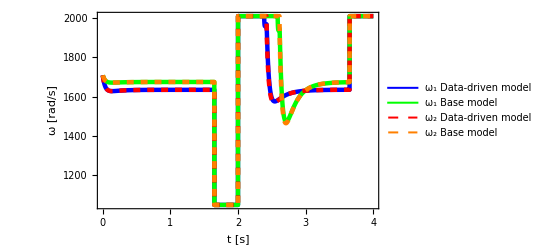

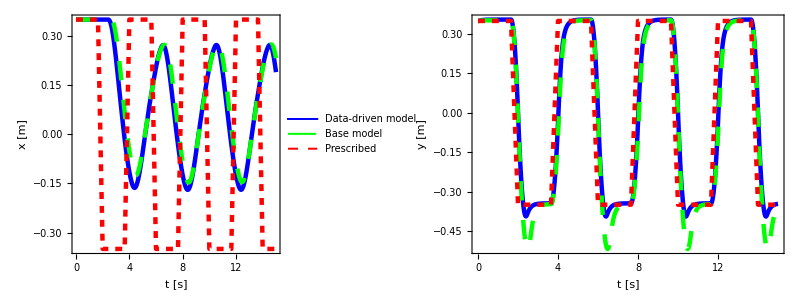

```mathematica
vel=1;
A=0.35;
a=0.35;
xp[t_]:=Interpolation[Flatten[Table[{{2 i/vel,(-1)^i A},{2(i+1)/vel-a,(-1)^i A}},{i,0,IntegerPart[T/2]}],1],t,InterpolationOrder->1]
yp[t_]:=Interpolation[Flatten[Table[{{2 i/vel,(-1)^i A},{2(i+1)/vel-a,(-1)^i A}},{i,0,IntegerPart[T/2]}],1],t,InterpolationOrder->1];
T=15;
sol=Simulate[xp[t],yp[t],T,{A,A,0,0,0,0}];
diff[sol,xp,yp,T,T]
popla035=PlotOmega[sol,{{0,4},{2,T}},True]
pxypla035=Plotxy[sol,{0,T}]
```

```mathematica
Export[FileNameJoin[{dir,"fig/out_pl_orig_disp035.png"}],pxypla035,ImageResolution->500];
```

### a=0.3

<|orig,x→324.727,new,x→152.635,orig,y→21.1679,new,y→19.6994,orig,disp→32.4607,new,disp→8.41893|>

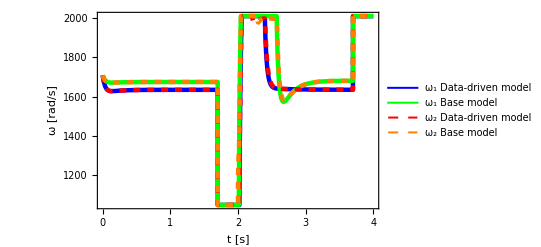

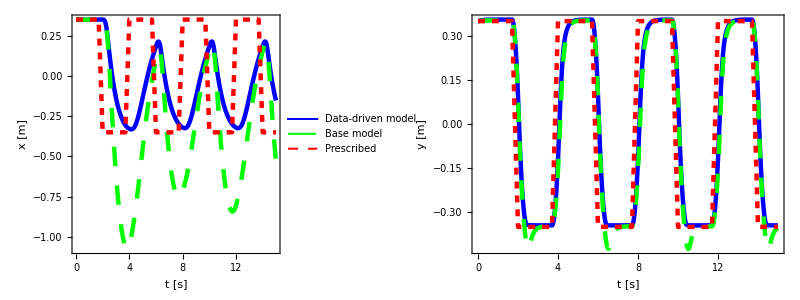

```mathematica
vel=1;
A=0.35;
a=0.3;
xp[t_]:=Interpolation[Flatten[Table[{{2 i/vel,(-1)^i A},{2(i+1)/vel-a,(-1)^i A}},{i,0,IntegerPart[T/2]}],1],t,InterpolationOrder->1]
yp[t_]:=Interpolation[Flatten[Table[{{2 i/vel,(-1)^i A},{2(i+1)/vel-a,(-1)^i A}},{i,0,IntegerPart[T/2]}],1],t,InterpolationOrder->1];
T=15;
sol=Simulate[xp[t],yp[t],T,{A,A,0,0,0,0}];
diff[sol,xp,yp,T,T]
popla03=PlotOmega[sol,{{0,4},{2,T}},True]
pxypla03=Plotxy[sol,{0,T}]
```

```mathematica
popl=Legended[Grid[{First/@{popla035,popla03}}],Last@popla03];
Export[FileNameJoin[{dir,"fig/out_pl_orig_disp03.png"}],pxypla03,ImageResolution->500];
Export[FileNameJoin[{dir,"fig/out_pl_orig_omega.png"}],popl,ImageResolution->500];
```

## Piecewise linear square phase shift

### a=0.4

<|orig,x→94.4867,new,x→86.39,orig,y→28.5585,new,y→15.1468,orig,disp→13.8351,new,disp→8.13496|>

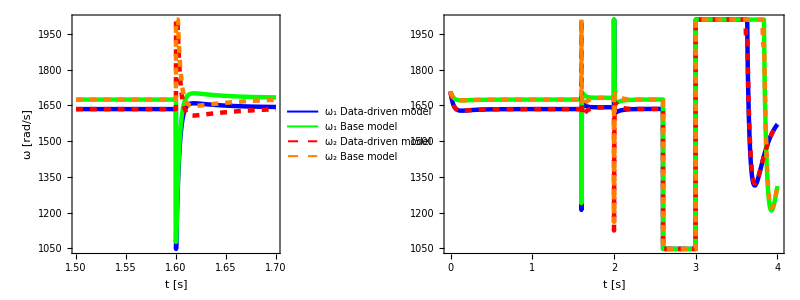

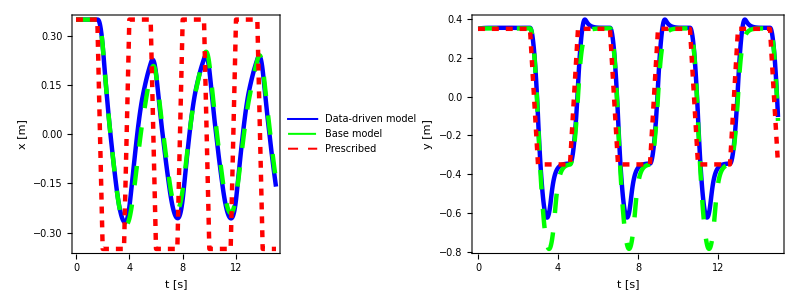

```mathematica
vel=1;
A=0.35;
a=0.4;
xp[t_]:=Interpolation[Flatten[Table[{{2 i/vel,(-1)^i A},{2(i+1)/vel-a,(-1)^i A}},{i,0,IntegerPart[T/2]}],1],t,InterpolationOrder->1]
yp[t_]:=Interpolation[Flatten[{{{{0,A}}},Table[{{2 i/vel+1,(-1)^i A},{2(i+1)/vel+1-a,(-1)^i A}},{i,0,IntegerPart[T/2]}]},2],t,InterpolationOrder->1];
T=15;
sol=Simulate[xp[t],yp[t],T,{A,A,0,0,0,0}];
diff[sol,xp,yp,T,T]
poplpa04=PlotOmega[sol,{{1.5,1.7},{0,4}}]
pxyplpa04=Plotxy[sol,{0,T}]
```

```mathematica
Export[FileNameJoin[{dir,"fig/out_plp_orig_disp04.png"}],pxyplpa04,ImageResolution->500];
Export[FileNameJoin[{dir,"fig/out_plp_orig_omega04.png"}],poplpa04,ImageResolution->500];
```

### a=0.35

<|orig,x→89.2976,new,x→95.3535,orig,y→16.9827,new,y→14.3841,orig,disp→8.16542,new,disp→8.6794|>

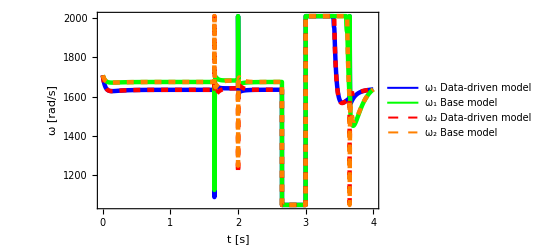

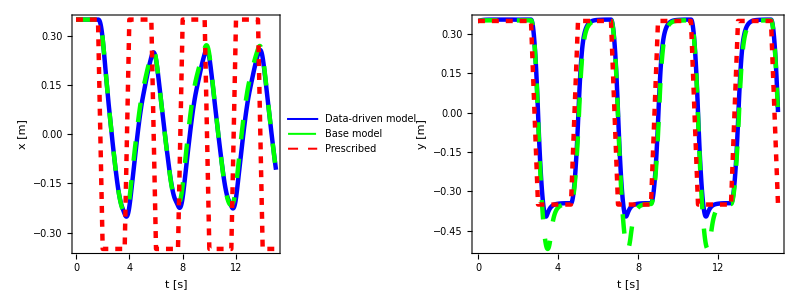

```mathematica
vel=1;
A=0.35;
a=0.35;
xp[t_]:=Interpolation[Flatten[Table[{{2 i/vel,(-1)^i A},{2(i+1)/vel-a,(-1)^i A}},{i,0,IntegerPart[T/2]}],1],t,InterpolationOrder->1]
yp[t_]:=Interpolation[Flatten[{{{{0,A}}},Table[{{2 i/vel+1,(-1)^i A},{2(i+1)/vel+1-a,(-1)^i A}},{i,0,IntegerPart[T/2]}]},2],t,InterpolationOrder->1];
T=15;
sol=Simulate[xp[t],yp[t],T,{A,A,0,0,0,0}];
diff[sol,xp,yp,T,T]
poplpa035=PlotOmega[sol,{{0,4},{2,T}},True]
pxyplpa035=Plotxy[sol,{0,T}]
```

```mathematica
Export[FileNameJoin[{dir,"fig/out_plp_orig_disp035.png"}],pxyplpa035,ImageResolution->500];
```

### a=0.3

<|orig,x→96.7117,new,x→102.648,orig,y→19.8045,new,y→18.6363,orig,disp→9.24422,new,disp→9.79101|>

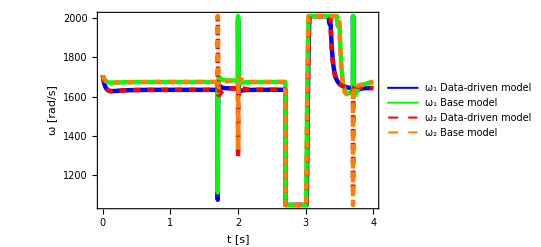

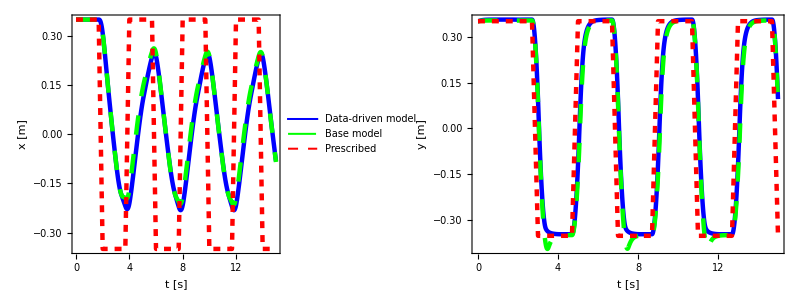

```mathematica
vel=1;
A=0.35;
a=0.3;
xp[t_]:=Interpolation[Flatten[Table[{{2 i/vel,(-1)^i A},{2(i+1)/vel-a,(-1)^i A}},{i,0,IntegerPart[T/2]}],1],t,InterpolationOrder->1]
yp[t_]:=Interpolation[Flatten[{{{{0,A}}},Table[{{2 i/vel+1,(-1)^i A},{2(i+1)/vel+1-a,(-1)^i A}},{i,0,IntegerPart[T/2]}]},2],t,InterpolationOrder->1];
T=15;
sol=Simulate[xp[t],yp[t],T,{A,A,0,0,0,0}];
diff[sol,xp,yp,T,T]
poplpa03=PlotOmega[sol,{{0,4},{2,T}},True]
pxyplpa03=Plotxy[sol,{0,T}]
```

```mathematica
poplp=Legended[Grid[{First/@{poplpa035,poplpa03}}],Last@poplpa03];
Export[FileNameJoin[{dir,"fig/out_plp_orig_disp03.png"}],pxyplpa03,ImageResolution->500];
Export[FileNameJoin[{dir,"fig/out_plp_orig_omega.png"}],poplp,ImageResolution->500];
```

## Smooth

## Smooth1

<|orig,x→14.6173,new,x→61.2709,orig,y→0.0382267,new,y→0.131109,orig,disp→0.0760442,new,disp→0.164231|>

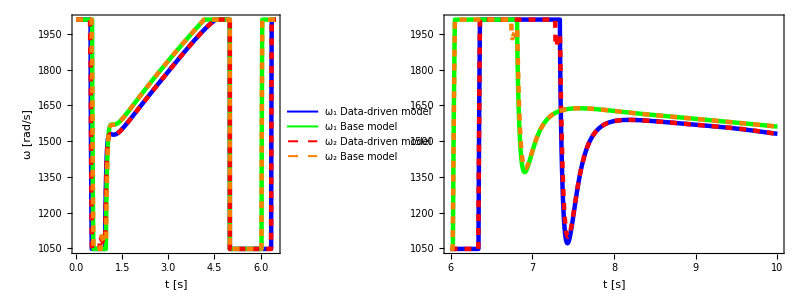

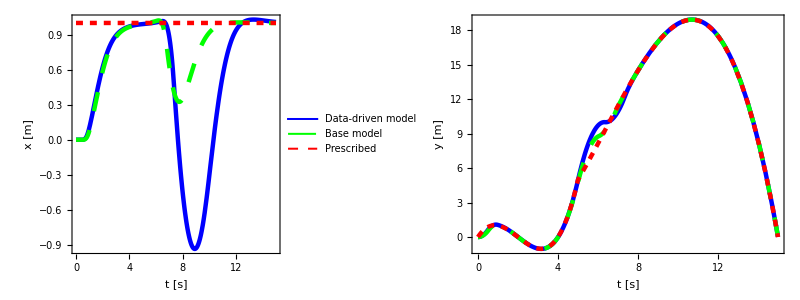

```mathematica
vel=1;
A=0.35;
a=0.3;
xp[t_]:=1;
yp[t_]:=Interpolation[{{0,0},{1,1},{2,0},{5,5},{15,0}},t] ;
T=15;
sol=Simulate[xp[t],yp[t],T,{0,0,0,0,0,0}];
diff[sol,xp,yp,T,T]
posm1=PlotOmega[sol,{{0,6.5},{6,10}}]
pxysm1=Plotxy[sol,{0,T}]
```

```mathematica
Export[FileNameJoin[{dir,"fig/out_sm1_orig_disp.png"}],pxysm1,ImageResolution->500];
Export[FileNameJoin[{dir,"fig/out_sm1_orig_omega.png"}],posm1,ImageResolution->500];
```

## Smooth2

<|orig,x→66.4888,new,x→0.182558,orig,y→88.2921,new,y→60.5957,orig,disp→64.9812,new,disp→0.483721|>

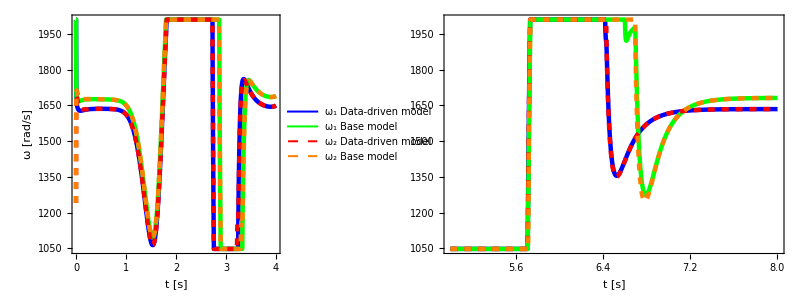

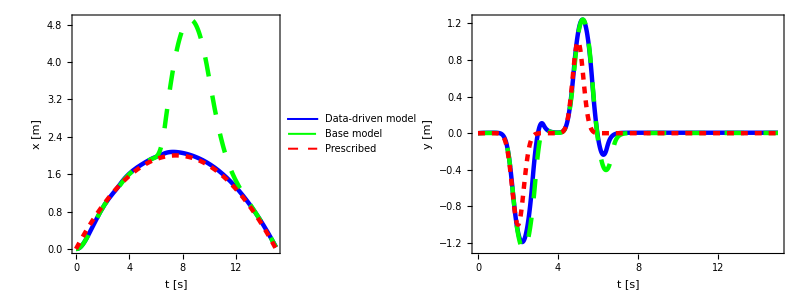

```mathematica
vel=1;
A=0.35;
a=6;
b=7;
xp[t_]:=(-(t-7.5)^2/7.5^2+1)*2;
yp[t_]:=-ⅇ^(-a*(t-2)^2)+ⅇ^(-b*(t-5)^2);
T=15;
sol=Simulate[xp[t],yp[t],T,{0,0,0,0,0,0}];
diff[sol,xp,yp,T,T]
posm2=PlotOmega[sol,{{0,4},{5,8}}]
pxysm2=Plotxy[sol,{0,T}]
```

```mathematica
Export[FileNameJoin[{dir,"fig/out_sm2_orig_disp.png"}],pxysm2,ImageResolution->500];
Export[FileNameJoin[{dir,"fig/out_sm2_orig_omega.png"}],posm2,ImageResolution->500];
```